```mathematica
ClearAll["Global`*"];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];

Get[NotebookDirectory[]<>"H1Data.m"];
Get[ParentDirectory[NotebookDirectory[]]<>"/Functions.m"];
```

Fusion rules

```mathematica
TableForm[Table[Sum[V[a,b][c]objNames[c],{c,obs}],{a,obs},{b,obs}],TableHeadings->{objNames[#]&/@obs,objNames[#]&/@obs}]
```

| 1 | μ | η | ν
1 | 1 | μ | η | ν
μ | μ | 1+ν | η+ν | η+μ+ν
η | η | η+ν | 1+η+μ+ν | η+μ+2 ν
ν | ν | η+μ+ν | η+μ+2 ν | 1+2 η+μ+2 ν

#### Dimensions

```mathematica
dim[#]&/@obs
dtot[]^2
```

{1,1/2 (1+√13),1/2 (3+√13),1/2 (5+√13)}

3/2 (13+3 √13)

#### Frobenius-Schur indicators

```mathematica
κ[#]&/@obs
```

{1,1,1,1}

#### Unitary fusion category?

```mathematica
NpentagonQ&&NunitaryQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

#### Visualizations

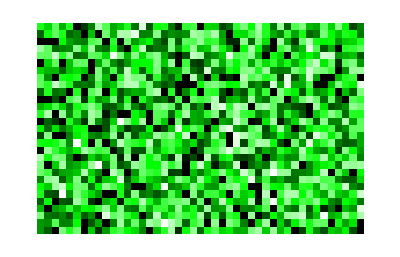

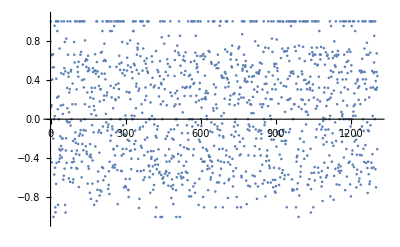

```mathematica
ArrayPlot[ArrayReshape[RandomSample[(Fs+1)/2],{29,45},∞],ColorFunction-> (Blend[{White,Green,Black},#]&),Frame->False,ColorFunctionScaling->False]
ListPlot[RandomSample[Fs],PlotRange->{-1.05,1.05}]
```

```mathematica
Fblk[3,3,3][3]//MatrixForm
```

(1/6 (5-√13) | Root0.353Root[-3+23 #1^2+9 #1^4&,2]0.3526769790748032 | Root-0.370Root[1-11 #1^2+27 #1^4&,2]-0.3700462614857172 | Root0.204Root[-1+23 #1^2+27 #1^4&,2]0.20361814880582163 | Root0.204Root[-1+23 #1^2+27 #1^4&,2]0.20361814880582163 | Root0.370Root[1-11 #1^2+27 #1^4&,3]0.3700462614857172 | Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | 0 | 0 | Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563
Root0.353Root[-3+23 #1^2+9 #1^4&,2]0.3526769790748032 | 1/2 (-3+√13) | Root0.522Root[1-846 #1^2+4059 #1^4-5346 #1^6+6561 #1^8&,4]0.5221873879909109 | Root-0.134Root[1-57 #1^2+81 #1^4&,2]-0.13418089108033268 | Root-0.134Root[1-57 #1^2+81 #1^4&,2]-0.13418089108033268 | Root0.0345Root[1-846 #1^2+4059 #1^4-5346 #1^6+6561 #1^8&,3]0.03447902409206689 | Root0.471Root[-507+2236 #1^2+243 #1^4&,2]0.4705489506108513 | Root0.237Root[3-67 #1^2+243 #1^4&,3]0.2371770534233195 | Root0.237Root[3-67 #1^2+243 #1^4&,3]0.2371770534233195 | Root-0.374Root[-16+12 #1^2+729 #1^4&,1]-0.37436097956812947
Root0.422Root[-1+4 #1^2+9 #1^4&,2]0.42236783277454437 | Root-0.522Root[1-846 #1^2+4059 #1^4-5346 #1^6+6561 #1^8&,1]-0.5221873879909109 | Root0.149Root[1-18 #1+144 #1^2-567 #1^3+729 #1^4&,1]0.14857811152703682 | Root0.0343Root[1-891 #1^2+34344 #1^4-223074 #1^6+531441 #1^8&,3]0.03428061623086858 | Root0.0343Root[1-891 #1^2+34344 #1^4-223074 #1^6+531441 #1^8&,3]0.03428061623086858 | Root0.273Root[-17-6 #1+306 #1^2-405 #1^3+729 #1^4&,2]0.273178143027734 | Root0.159Root[16-96 #1-56 #1^2+54 #1^3+729 #1^4&,1]0.15903318431217653 | Root-0.145Root[1-67 #1^2+3028 #1^4-112266 #1^6+531441 #1^8&,2]-0.14450979849299014 | Root-0.627Root[841-297001 #1^2+1238656 #1^4-1450710 #1^6+531441 #1^8&,1]-0.6265970527903857 | Root-0.105Root[-43-480 #1-342 #1^2+3888 #1^3+6561 #1^4&,1]-0.10523862965020826
0 | Root-0.134Root[1-57 #1^2+81 #1^4&,2]-0.13418089108033268 | Root0.336Root[1+27 #1^2+324 #1^4-65610 #1^6+531441 #1^8&,4]0.3357656452548486 | Root0.399Root[-23-57 #1+9 #1^2+405 #1^3+729 #1^4&,2]0.39932691824822175 | Root0.399Root[-23-57 #1+9 #1^2+405 #1^3+729 #1^4&,2]0.39932691824822175 | Root-0.287Root[2401-144207 #1^2+1534140 #1^4-1718982 #1^6+531441 #1^8&,1]-0.2871108866340618 | Root0.174Root[-9+277 #1^2+729 #1^4&,2]0.1735098490191538 | Root-0.596Root[-17+75 #1-101 #1^2-27 #1^3+729 #1^4&,1]-0.5957260159419993 | Root0.280Root[-17+75 #1-101 #1^2-27 #1^3+729 #1^4&,2]0.2803971941397781 | Root0.0654Root[-16+3708 #1^2+6561 #1^4&,2]0.06544114285527805
0 | Root0.134Root[1-57 #1^2+81 #1^4&,3]0.13418089108033268 | Root0.146Root[2401-144207 #1^2+1534140 #1^4-1718982 #1^6+531441 #1^8&,3]0.14632160904254704 | Root0.477Root[-23+57 #1+9 #1^2-405 #1^3+729 #1^4&,2]0.47679629183355565 | Root0.477Root[-23+57 #1+9 #1^2-405 #1^3+729 #1^4&,2]0.47679629183355565 | Root-0.195Root[1+27 #1^2+324 #1^4-65610 #1^6+531441 #1^8&,2]-0.1949763676633338 | Root-0.174Root[-9+277 #1^2+729 #1^4&,1]-0.1735098490191538 | Root0.596Root[-17-75 #1-101 #1^2+27 #1^3+729 #1^4&,2]0.5957260159419993 | Root-0.280Root[-17-75 #1-101 #1^2+27 #1^3+729 #1^4&,1]-0.2803971941397781 | Root-0.0654Root[-16+3708 #1^2+6561 #1^4&,1]-0.06544114285527805
Root-0.422Root[-1+4 #1^2+9 #1^4&,1]-0.42236783277454437 | Root0.0345Root[1-846 #1^2+4059 #1^4-5346 #1^6+6561 #1^8&,3]0.03447902409206689 | Root0.196Root[-17+6 #1+306 #1^2+405 #1^3+729 #1^4&,2]0.1957087694424001 | Root-0.175Root[1-891 #1^2+34344 #1^4-223074 #1^6+531441 #1^8&,1]-0.17506989382238336 | Root-0.175Root[1-891 #1^2+34344 #1^4-223074 #1^6+531441 #1^8&,1]-0.17506989382238336 | Root-0.441Root[1+18 #1+144 #1^2+567 #1^3+729 #1^4&,1]-0.4406191815542959 | Root0.472Root[16-96 #1-56 #1^2+54 #1^3+729 #1^4&,2]0.47162445929226593 | Root0.0535Root[841-297001 #1^2+1238656 #1^4-1450710 #1^6+531441 #1^8&,3]0.053532950543367895 | Root-0.429Root[1-67 #1^2+3028 #1^4-112266 #1^6+531441 #1^8&,1]-0.4285543037540277 | Root0.343Root[-43-480 #1-342 #1^2+3888 #1^3+6561 #1^4&,2]0.34309807786709556
Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | Root0.471Root[-507+2236 #1^2+243 #1^4&,2]0.4705489506108513 | Root-0.223Root[-29-28 #1+289 #1^2-594 #1^3+729 #1^4&,1]-0.2229795506563106 | Root-0.0753Root[-1+172 #1^2+729 #1^4&,1]-0.07534813473623674 | Root-0.0753Root[-1+172 #1^2+729 #1^4&,1]-0.07534813473623674 | Root-0.497Root[-29+28 #1+289 #1^2+594 #1^3+729 #1^4&,1]-0.4968480219354221 | 1/81 (121-38 √13) | Root-0.307Root[-81+244 #1^2+6561 #1^4&,1]-0.3066946000951085 | Root-0.307Root[-81+244 #1^2+6561 #1^4&,1]-0.3066946000951085 | 1/162 (1-5 √13)
0 | Root0.237Root[3-67 #1^2+243 #1^4&,3]0.2371770534233195 | Root0.414Root[81-1026 #1^2-6236 #1^4-35721 #1^6+531441 #1^8&,4]0.4138003078829543 | 1/27 (-22+2 √13) | 1/27 (5+2 √13) | Root0.240Root[81-1026 #1^2-6236 #1^4-35721 #1^6+531441 #1^8&,3]0.24029045886380046 | Root-0.307Root[-81+244 #1^2+6561 #1^4&,1]-0.3066946000951085 | 1/162 (1-5 √13) | 1/162 (1-5 √13) | Root0.307Root[-81+244 #1^2+6561 #1^4&,2]0.3066946000951085
0 | Root0.237Root[3-67 #1^2+243 #1^4&,3]0.2371770534233195 | Root0.414Root[81-1026 #1^2-6236 #1^4-35721 #1^6+531441 #1^8&,4]0.4138003078829543 | 1/27 (5+2 √13) | 1/27 (-22+2 √13) | Root0.240Root[81-1026 #1^2-6236 #1^4-35721 #1^6+531441 #1^8&,3]0.24029045886380046 | Root-0.307Root[-81+244 #1^2+6561 #1^4&,1]-0.3066946000951085 | 1/162 (1-5 √13) | 1/162 (1-5 √13) | Root0.307Root[-81+244 #1^2+6561 #1^4&,2]0.3066946000951085
Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | Root-0.374Root[-16+12 #1^2+729 #1^4&,1]-0.37436097956812947 | Root0.0607Root[53-1050 #1+3087 #1^2-3402 #1^3+6561 #1^4&,1]0.060653665156563154 | Root-0.108Root[-1+9 #1^2+6561 #1^4&,1]-0.10806870616387576 | Root-0.108Root[-1+9 #1^2+6561 #1^4&,1]-0.10806870616387576 | Root-0.332Root[53+1050 #1+3087 #1^2+3402 #1^3+6561 #1^4&,1]-0.332144530230992 | 1/162 (1-5 √13) | Root0.307Root[-81+244 #1^2+6561 #1^4&,2]0.3066946000951085 | Root0.307Root[-81+244 #1^2+6561 #1^4&,2]0.3066946000951085 | 1/81 (-14+16 √13))